```mathematica
Clear[Ν,X,Y,Z,H,Ι,J,λ,Κ,s,GenerateSValues,A,B,Α,Β];
```

```mathematica
(* Physical constants *)
k=1.38065 10^-23;
T=Quantity[15.5 10^-3,"Kelvin"];
ℏ=6.62607 10^-34;
β=1/(k T);
(* D Wave anneal parameters *)
DWaveAnnealingSchedule=Import["~/Dropbox/Redfield/src/data/DWaveAnnealingSchedule.csv"][[;;,1;;3]];
AnnealParameter=DWaveAnnealingSchedule[[;;,1]];
A=10^9 DWaveAnnealingSchedule[[;;,2]];     (* units in GHz *)
B=10^9 DWaveAnnealingSchedule[[;;,3]];
(* Pauli Matrices *)
Ν=8;
X=Table[
Apply[KroneckerProduct][
Table[
If[k==j,PauliMatrix[1],IdentityMatrix[2]],{k,1,Ν}]
],{j,1,Ν}];
Y=Table[
Apply[KroneckerProduct][
Table[
If[k==j,PauliMatrix[2],IdentityMatrix[2]],{k,1,Ν}]
],{j,1,Ν}];
Z=Table[
Apply[KroneckerProduct][
Table[
If[k==j,PauliMatrix[3],IdentityMatrix[2]],{k,1,Ν}]
],{j,1,Ν}];

Α=Interpolation[Transpose@{AnnealParameter,A},InterpolationOrder->1];

Β=Interpolation[Transpose@{AnnealParameter,B},InterpolationOrder->1];

(* Definition of D Wave Hamiltonian *)

Clear[J,Κ]
λ[Ν_,{J_,Κ_}]=Which[OddQ[Ν],

Table[If[k==⌊Ν/2⌋ ∨ k==⌈Ν/2⌉,J,Κ],{k,1,Ν-1}],

EvenQ[Ν],

Table[If[k==Ν/2∨ k==Ν/2+1,J,Κ],{k,1,Ν-1}]
];


H[s_,{Ι_,J_,Κ_}]:=

2π (Α[s]/2∑_(k=1)^Ν X[[k]]-Β[s]/2(-Ι Z[[-1]].Z[[1]]+∑_(k=1)^(Ν-1) λ[Ν,{J,Κ}][[k]]Z[[k]].Z[[k+1]]));

getIndex[orderedList_,val_]:=Module[{test},
test=1;
While[val<orderedList[[test]],
test=test+1;
];
test
];

GenerateDiscretization[tQA_,{Ι_,J_,Κ_},{step_,windowSize_,numSamples_}]:=Module[{sVals,tVals,badSvals,gammab,gammaVals, bindex,sb,rb,mingap,middleMax,middleMin,middleSvals,startMax,startMin,startSvals,endMax,endMin,endSvals,startUsed,endUsed},
sVals=Range[0,1,step];
tVals=(tQA#)&/@sVals;
badSvals={1};

If[Ι Κ > J^2,
gammab=((Κ^2-J^2)(J^2-Ι^2))/(Ι(Ι^2+Κ^2-2 J^2));
gammaVals=Α[#]/Β[#]&/@sVals;
bindex=getIndex[gammaVals,gammab];
sb=sVals[[bindex]];
(*Print[gammab];
Print[gammaVals];
Print[bindex];*)
rb=(Κ(J^2-Ι^2))/(Ι(Κ^2-J^2));
mingap=0.05 rb^((Ν-5)/2);
middleMin=Max[sb-windowSize mingap,0];
middleMax=Min[sb+windowSize mingap,1];
middleSvals=Range[middleMin,middleMax,(middleMax-middleMin)/numSamples];
(*Print[mingap];*)
(*Print[middleMin];
Print[middleMax];*)
startMin=0;
startMax=middleMin;
startSvals=Range[startMin,startMax,step];

endMin=middleMax;
endMax=1;
endSvals=Range[endMin,endMax,step];

startUsed=(middleMin>0);
endUsed=(middleMax<1);
If[startUsed,
sVals =Sort[Catenate[{startSvals,middleSvals}]];
badSvals=Catenate[{badSvals,{Length[startSvals]}}];
If[endUsed,
sVals =Sort[Catenate[{sVals,endSvals[[2;;]]}]];
badSvals=Catenate[{badSvals,{Length[startSvals]+Length[middleSvals]}}];
];
,
If[endUsed,
sVals=Sort[Catenate[{middleSvals,endSvals}]];
badSvals=Catenate[{badSvals,{Length[middleSvals]}}];
];
];
badSvals=Catenate[{badSvals,{Length[sVals]}}];
tVals=(tQA#)&/@sVals;
,
Print["Bottleneck Does Not Exist. Outputting Normal Resolution."];
];
{sVals,badSvals,tVals}
];
```

```mathematica
M[{Hbefore_,Hafter_},Nc_,dt_]:=Module[{ϕp1,ϕm1,ϵp1,ϵm1,bkt},
{ϵp1,ϕp1}=Eigensystem[Hafter];
{ϵp1,ϕp1}={ϵp1[[#]],ϕp1[[#]]}&@Ordering[ϵp1];

{ϵm1,ϕm1}=Eigensystem[Hbefore];
{ϵm1,ϕm1}={ϵm1[[#]],ϕm1[[#]]}&@Ordering[ϵm1];

Print[(ϕp1[[1]]+ϕm1[[1]]).(ϕp1[[2]]-ϕm1[[2]])//MatrixForm];
bkt[n_,m_]:=1/(4dt)(ϕp1[[n]]+ϕm1[[n]]).(ϕp1[[m]]-ϕm1[[m]]);
(*Print[bkt[1,2]];*)

Table[KroneckerDelta[i,k]bkt[l,j]+KroneckerDelta[j,l]bkt[k,i],
{i,1,Nc},{j,1,Nc},{k,1,Nc},{l,1,Nc}]
];
Ω[ϵ_,Nc_]:=Table[-ⅈ KroneckerDelta[i,k]KroneckerDelta[j,l](ϵ[[i]]-ϵ[[j]]),{i,1,Nc},{j,1,Nc},{k,1,Nc},{l,1,Nc}];
```

```mathematica
s=.235;Ι=.2;J=.3;Κ=1;Nc=5;
Hbefore=H[s,{Ι,J,Κ}];
Hafter=H[s+0.001,{Ι,J,Κ}];
dt=5 10^-15;
```

```mathematica
Moutput=M[{Hbefore,Hafter},Nc,dt];
```

1.54119×10^-16

```mathematica
For[i=1,i≤ Nc,i++,
For[j=1,j≤ Nc,j++,
For[k=1,k≤ Nc,k++,
For[l=1,l≤ Nc,l++,
Print[{i-1,j-1,k-1,l-1}];
Print[Moutput[[i,j,k,l]]];
];
];
];
];
```

0.041899

```mathematica
kB=1.381 10^-23;
ℏ=(6.626070000000001*^-34)/(2π);
T=15.5 10^-3;
```

```mathematica
ℏ
```

1.05457×10^-34

```mathematica
ηMRT=0.24;
η[s_]:=
ηMRT Β[s]/Β[1];
S[ω_,s_]:=Which[
Abs[ω]>10^11,0,
ω==0,(kB T)/ℏ η[s],
True,(η[s] ω)/(1-Exp[-ℏ ω/(kB T)])];
δ[i_,j_]:=KroneckerDelta[i,j];
Ζ[μ_,i_,j_]:=Z[[μ]].ϕ
R[ϵ_,ϕ_,s_,Nc_]:=Module[{A,ω},
A[μ_,i_,j_]:=ϕ[[j]].Z[[μ]].ϕ[[i]];
ω[i_,j_]:=ϵ[[i]]-ϵ[[j]];
Table[
-1/2∑_(μ=1)^Ν (δ[b,d]∑_(n=1)^Nc A[μ,a,n]A[μ,n,c]S[ω[c,n],s]-A[μ,a,c]A[μ,d,b]S[ω[c,a],s]+δ[a,c]∑_(n=1)^Nc A[μ,d,n]A[μ,n,b]S[ω[c,n],s]-A[μ,a,c]A[μ,d,b]S[ω[d,b],s]),
{a,1,Nc},{b,1,Nc},{c,1,Nc},{d,1,Nc}]
];
```

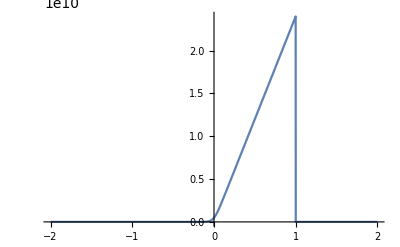

```mathematica
Plot[S[ω,1],{ω,-2 10^11,2 10^11},PlotRange->All]
```

```mathematica
S[0,1]
```

4.87147×10^8

```mathematica
s=.524;Ι=.3;J=.9;Κ=1.4;Nc=3;
Hnow=H[s,{Ι,J,Κ}];
{ϵ,ϕ}=Eigensystem[Hnow];
{ϵ,ϕ}={ϵ[[#]],ϕ[[#]]}&@Ordering[ϵ];
```

```mathematica
Routput=R[ϵ,ϕ,s,Nc];//AbsoluteTiming
```

{3.92862,Null}

```mathematica
For[i=1,i≤ Nc,i++,
For[j=1,j≤ Nc,j++,
For[k=1,k≤ Nc,k++,
For[l=1,l≤ Nc,l++,
Print[{i-1,j-1,k-1,l-1}];
Print[Routput[[i,j,k,l]]];
];
];
];
];
```

```mathematica
ρ
```

```mathematica
s=.235;Ι=.2;J=.3;Κ=1;Nc=5;
Hnow=H[s,{Ι,J,Κ}];
{ϵ,ϕ}=Eigensystem[Hnow];
{ϵ,ϕ}={ϵ[[#]],ϕ[[#]]}&@Ordering[ϵ];

Table[ⅇ^((-ℏ (ϵ[[j]]-ϵ[[1]]))/(kB T)),{j,1,Nc}]//TableForm
```

1.
6.15174×10^-6
4.56328×10^-6
1.34072×10^-6
7.54065×10^-7